# What is Going on in Biology? The Wolframian Perspective

What is the nature of biological processes? How do they look? What can they achieve? What happens when they go wrong?  These are such simple questions, and yet the field of biology, in my view, has largely failed to give people good answers. 

In my experience, modern academic institutions are really bad at answering big questions like this, and most of the best “scientists” of our time have found ways to make progress not because of these institutions but despite them. 

So okay these are bold statements, who do I think I am, right? Well, I think most biologists have largely missed a powerful new class of models: those based on simple computational rules. And because of this, they have been limited in their ability to give good high-level descriptions of what is going on in biology. 

For thirty years now, Stephen Wolfram has been filling this gap, and pioneered some groundbreaking computational models for biological systems. Starting as a fan of the research, and eventually becoming a collaborator, I’ve become convinced that with Wolfram’s models, we’ve struck gold, and are now in a position to understand and communicate the high-level features of biology better than ever before. 

Despite this, most people outside of the Wolfram circle don’t know about his work in biology. So, because we believe its so important, myself and others at the Wolfram Institute thought it would be a good idea to bring all of Wolfram’s work in biology into one place, so that those who are curious can get up to speed as fast as possible. 

Stephen has published a ton of work that is very accessible, and I will link to it as we go. And I think just going through the references and exploring what’s interesting to you is also a reasonable approach. 

But my goal with this article is to provide a single chronological and theoretical thread through his research in theoretical biology. Even by telling this story, I’ve felt my intuition for biology growing. Not only that, I’ve felt that understanding Stephen’s biological work in its entirety, has helped me better understand what makes sense to do next. And my hope, is that the reader will have a similar experience. 

Okay, so, where to start? The first important piece of the story is understanding Stephen himself, so who the hell is this guy? And what makes him special?

### Stephen’s Backstory

From my observations and interactions with Stephen at Wolfram Summer School and working with him on the medicine post, my impression is he was basically born to be a scientist. 

The one sentence summary is that he’s just an extremely curious, intelligent, friendly, and independent-minded person. This combination is very unique, and so it makes him a powerful force in the world of science and technology.

In addition to Stephen’s talent though, I believe his story can also tell us a lot about what makes his research in biology different.

So what was that story? 

Well, he’s been doing serious science since he was a teenager. He famously got interested in the second law of thermodynamics from this textbook on the subject at the age of twelve:

```mathematica
-Graphics--Graphics-
```

The book, was unique from other physics books in that its conclusions did not require a trust in authority, rather one could “reach the truth” simply by understanding the ideas in the book.  In Stephen’s words “what was so exciting that day was that I got a first taste of the idea that one didn’t have to be told how the world works; one could just figure it out”:

This idea, that the arrangement of gas particles tends towards disorder, was also his first introduction to the “science of complexity” (although it didn’t have that name at the time) and importantly for us, it was this interest that would eventually lead him to model the origin of complexity in biological systems. This connection, was by no means a linear path though. 

He spent his teens and early twenties deep in the field of particle physics. While very far from biology, it was during this time, he figured out that computers could be useful for doing science, often using them to do physics calculations. And this appreciation for the computer as a tool for science would grow and become an essential theme in his future work, including, in biology.

In his words, Stephen “quickly outgrew” the computational tools he was using. And after getting his phD in physics, he decided to work on building a software system that could, once-and-for-all, fulfill all his scientific needs. 

This famously turned into Mathematica, which ended up being extremely useful for Stephen (and others) in doing science. But more than being a useful tool, the process of building Mathematica continued to help develop Wolfram’s intuition that many of these “human creations” like mathematical equations, and the models of physics, could indeed be boiled down to computational rules ((check that this is the right way to put this)).

((Ask if I can use this https://www.wolfram.com/mathematica/scrapbook/)

With this powerful new tool and understanding, and with the rapid improvement of computers, Stephen began to separate himself from the traditions of physics, mostly using computational models instead of mathematical ones. 

But what did all this mean for his childhood interest in complexity? Well after having success with Mathematica by stripping things down to their computational essentials, he began to use the same approach in his scientific endeavors. In particular, he started developing a “minimal model for complexity”. 

After repeatedly refining and simplifying, he arrived at what he would call a 1-dimensional cellular automata, some early print-outs of these 1D automata are shown below:

And with these powerful new minimal models, he began to make significant progress in answering his long held questions about the origin of complexity.

The first step, was the formulation of the concept of “computational irreducibility”. In exploring the behavior  of cellular automata, he started to realize that “unpredictability” was actually quite common, and he began to speculate about what that could mean for science. Here is an amusing piece of a transcript from the conference where he first spoke publicly about computational irreducibility:

The next crucial step, came from Rule 30. Interestingly, Stephen had looked at Rule 30 two years earlier in 1982, but he hadn’t yet understood its importance. After more study of cellular automata and after printing it out in higher resolution, its significance hit him, and he realized, that surprisingly, complex phenomena can originate not just from complex programs but even from simple ones. Here we show the earlier low resolution printout of Rule 30 on the left and the higher resolution one on the right:

```mathematica
-Graphics--Graphics-
```

And seeing these two images side-by-side, you can see why the second one was what made things click. What Rule 30 so beautifully shows, is that, starting from a simple initial condition (with one black cell) and running a simple set of rules (eight rules in this case) one can already generate complex, or random behavior.

Digressing slightly, this story also nicely illustrates how the accessibility of Stephen’s models played an important role in expediting his thinking.

I mentioned earlier that Wolfram was born to do science. But I also believe, that he was extremely lucky to find a path that enabled him to become well-versed in both the world of computation and the world of science. And it turned out, that there were a lot of low-hanging fruit in that intersection. 

In particular, nobody had captured the essence of complexity in such a simple model as in rule 30. And I think the fact that the model was so simple, gave him the mental clarity to realize its importance, and eventually connect the idea to so many different fields, as he did in New Kind of Science.

You might imagine that good ideas come from the mind, and the smartest minds have the best ideas. But even for someone as talented as Stephen, it was seeing the right picture that made all the difference in the formulation of his career-defining idea. 

And I’ve definitely experienced this phenomena in my own intellectual journey. Being able to readily visualize the behavior of cellular automata, I believe, has allowed me to understand things that I would’ve never understood otherwise, like the ubiquity of hierarchy in animals societies, or understanding why treating cancer is so difficult. Oddly enough, I can feel myself getting smarter by staring at looking at these computational creatures. 

Anyways, these two insights, computational irreducibility and the idea that simple programs can create complex behavior, were the seeds that grew into what would become New Kind of Science (NKS), where Stephen would make his first well-known foray into the field of theoretical biology.

### Biology in New Kind of Science

The connection to biology was quite straightforward (in retrospect at least); Given that simple programs could produce infinite complexity, Stephen speculated that much of the complex phenomena in biology was not a result of meticulous natural selection, but rather just a result of the fact that complexity was easy to generate.

But okay, what were some biological applications to Stephen’s newfound realization that complexity is abundant? One striking example he gives in NKS is in pigmentation patterns.

Pigmentation patterns of mollusc shells for example, in most species, are not exposed during the organisms lifetime and therefore have no effect on selection. But as you can see, from the array of shell images below, they patterns are very complex and look remarkably similar to the behavior of cellular automata.

-Graphics-

Here are some examples of cellular automata for comparison:

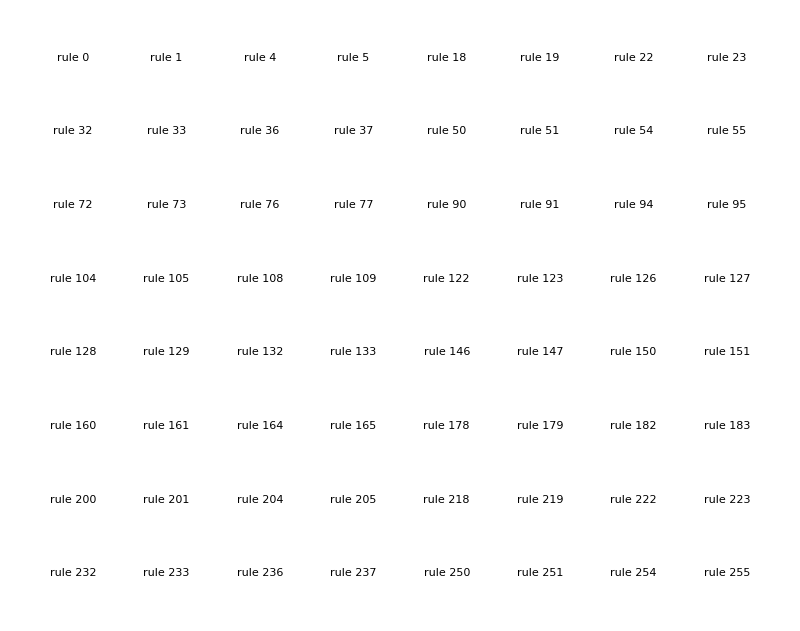

```mathematica
With[{srules=FromDigits[#,2]&/@Cases[Table[IntegerDigits[n,2,8],{n,0,255}],{_,a_,_,b_,a_,_,b_,_}],trand=BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,50]]},GraphicsGrid[Partition[Labeled[RulePlot[CellularAutomaton[#],trand,30,PlotRangePadding->None,ImageSize->90],Text[Style["rule "<>IntegerString[#],Italic]]]&/@srules,8],ImageSize->800]]
```

So what this example makes obvious, is that behaviors in biological systems aren’t always the result of natural selection: because the pigmentation patterns aren’t visible during the mollusc’s lifetime, we know there is no way of selection acting on them. Clearly, the complexity comes simply as a side-effect of the system responsible for generating pigmentation. And in fact, just like a cellular automata, mollusc shells can only grow on their edge, or “one line at a time”.

But okay, is this true for pigmentation in general, or just for mollusks? 

Looking at other branches in the tree of life, we can see that these automaton-like pigmentation patterns are not at all unique to molluscs:

And in fact, Stephen shows that one can imitate many of these pigmentation patterns using simple programs:

```mathematica
Layer[n_]:=Layer[n]=Select[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],MemberQ[#,n|-n]&]

Layer[n_,1]:=Layer[n,1]=Cases[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],{_,n|-n}]

Layer[n_,2]:=Layer[n,2]=Complement[Layer[n],Layer[n,1]]

SpotStep[w_List?VectorQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i]]Total[RotateLeft[list,#]&/@Layer[i]],{i,0,Length[w]-1}],{2}]

SpotStep[w_List?MatrixQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i,j]]Total[RotateLeft[list,#]&/@Layer[i,j]],{i,0,Length[w]-1},{j,2}],{2}]

SpotEvolveList[w_List,list_,n_]:=NestList[SpotStep[w,#]&,list,n]

GraphicsGrid[Table[MapIndexed[ArrayPlot[#1,FrameLabel->{None,Text[Style["step "<>Apply[IntegerString,#2],Italic]]}]&,SpotEvolveList[rule,BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,{60,60}]],6]],{rule,{{1,1,-0.4,-0.4},{1,1,-0.2,-0.2}}}],ImageSize->700]
```

-Graphics-

```mathematica
Layer[n_]:=Layer[n]=Select[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],MemberQ[#,n|-n]&]

Layer[n_,1]:=Layer[n,1]=Cases[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],{_,n|-n}]

Layer[n_,2]:=Layer[n,2]=Complement[Layer[n],Layer[n,1]]

SpotStep[w_List?VectorQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i]]Total[RotateLeft[list,#]&/@Layer[i]],{i,0,Length[w]-1}],{2}]

SpotStep[w_List?MatrixQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i,j]]Total[RotateLeft[list,#]&/@Layer[i,j]],{i,0,Length[w]-1},{j,2}],{2}]

SpotEvolveList[w_List,list_,n_]:=NestList[SpotStep[w,#]&,list,n]

GraphicsGrid[Table[MapIndexed[ArrayPlot[#1,FrameLabel->{None,Text[Style["step "<>Apply[IntegerString,#2],Italic]]}]&,SpotEvolveList[rule,BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,{60,60}]],6]],{rule,{{{1,1},{1,1},{-0.4,0},{-0.4,0}},{{1,1},{1,1},{0,-0.6},{0,-0.6}}}}],ImageSize->700]
```

-Graphics-

The above pictures show four evolutions of a 2D cellular automata. The first two rows use the same rule starting from slightly different random initial conditions. The second two rows use rules with different horizontal and vertical weights. The variation in the patterns here is remarkably similar to those we just saw in biology. This makes clear the idea that the variation observed in different pigmentation patterns can result from small changes to simple programs.

So okay, the complex pigmentation patterns in biology seem to be a side-effect of the simple programs that generate pigmentation.

But how do we know for sure that these complex pigmentation patterns aren’t a result of some careful evolutionary process?

To test this, Stephen looks at constraint satisfaction problems, in an attempt to evolve to something like a leopard print pattern. Starting with a random grid of cells, a single cell chosen randomly, is reversed ((check this)), if that cell does satisfy the local-constraint, then that change is kept, if it doesn’t then it is “rejected”.

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},Row[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,330}]&/@{<||>,<|{16,203}->0|>,<|{37,208}->3|>,<|{15,206}->0|>,<|{28,209}->2|>,<|{23,202}->3|>,<|{32,207}->0|>},Spacer[10],2],Spacer[1]]]
```

```mathematica
SeedRandom[3060];
ListLinePlot[ConstraintViolations/@NestList[With[{new=MapAt[1-#&,#,RandomInteger[{1,10},2]]},If[ConstraintViolations[new]>ConstraintViolations[#],#,new]]&,RandomChoice[{1,0},{10,10}],1000],Sequence[AspectRatio->1/8,PlotRange->{All,{0,65}},Filling->Axis,Frame->True,PlotRangePadding->0,ImageSize->Large,FrameTicks->{{Table[{n,Style[StringTemplate["``%"][100 (n/64)]]},{n,0,64,16}],False},{Automatic,False}}]]
```

```mathematica
CloudGet["https://wolfr.am/nks-page0345a-graphic"]
```

-Graphics-

And running this algorithm, what he finds is that inevitably evolution gets stuck at some local minima before it reaches an exact pattern:

And if you “relax the evolution”, by allowing “neutral” changes that don’t get you closer or further to satisfying the constraint, the solution may be reached, but only after an enormous amount of steps that would be infeasible for evolution. 

The takeaway here, is that evolution is limited in its ability to shape such systems. This strongly suggests that pigmentation patterns were not meticulously selected by some evolutionary process, and their complexity is just a side-effect. 

But going even further, and Stephen makes a point of this, evolution, because it has this problem of getting stuck in complex landscapes, rather than making things more complex, has the effect of making things simpler. 

The idea being that for simpler systems, it is easier to “push them” up some fitness hill, suggesting that evolution would “prefer” simpler systems. This claim as we’ll see, is a point of contention within Stephen’s work, and in his more recent work he essentially goes the other way. 

But before we discuss that, you may be thinking, this pigmentation stuff is interesting, but what about other systems in biology?

Well, one way Stephen answers this, is by looking at the shape of different organisms, one case that he explores in depth is the shapes of different leaves in the plant kingdom. 

Once again, he finds that the variation and complexity of leaf shape, can be modeled by simple programs, in this case, substitution programs with slightly different branching radii ((check this))

Suggesting that much like pigmentation, the observed variance and complexity in organism shape can be explained not just by natural selection, but rather by small changes in the underlying rules of simple programs.

To summarize the biological claim of New Kind of Science, we can imagine two views on biology. The first view, is that biological systems start as this simple goop. And evolution, is a patient and sober “sculptor”, meticulously removing bits of goop into these very specific shapes and patterns, that are chosen, because they are somehow more fit. 

An alternative view, is that instead, biological systems, from the start, are this wild, complex, hurricane of different parts, that are capable of a wide range of different behaviors. In this view, evolution is like an overwhelmed teacher, using the limited tools it has to keep the class from devolving into complete chaos. 

In the first “sculptor model”, the causality lies with evolution, and the observed phenomena can be traced back to natural selection. In the second “teacher model”, the causality mostly lies with the systems, and biological phenomena can be explained mostly by modeling the physical systems.

When New Kind of Science was published, the sculptor view was popular among biologists, and so Stephen made a point to emphasize the teacher view. Nowadays, the sculptor view is less common. 

I should note that this distinction is really the same as the distinction between evolutionary and developmental biology. And most of Wolfram’s models in New Kind of Science are on the side of developmental biology. Importantly for us, this has changed in his recent work, where he had a breakthrough in using cellular automata to model evolution, which we’ll discuss later. 

But clearly, both evolution and physical constraints are contributing to what’s observed in biology, and it’s really a question of how much to attribute to either side. What Stephen is saying in NKS, and what he still maintains with his new work, is that the field of biology tends to attribute too much of the observed behaviors to evolution, and not enough to the physical capabilities of the system. 

Okay so what is his new work?

For a long time, as mentioned, he spent more of his efforts on the developmental side of biology, rather than the evolutionary side. In attending biology conferences ((cite)) he would often think about what is the space of all possible rules like, and in NKS he actually noted that nearby rules did seem to have similar behavior. But, he never really had the intuition to think that this was worth exploring.

That changed when he started doing more in-depth modeling of machine learning ((cite)), and he started to get a sense for how these adaptive processes work (with Richard Assar). That, in combination with thinking about his friend Greg Chaitlin’s work relating the Busy Beaver problem to evolution, he decided to tried out some adaptive algorithms on cellular automata. In particular, he tried “evolving” to a cellular automata of length 50. And surprisingly, it worked:

And so

It basically came from his intuition with Richard Assar

### References

1. https://writings.stephenwolfram.com/2023/02/a-50-year-quest-my-personal-journey-with-the-second-law-of-thermodynamics/
2. https://writings.stephenwolfram.com/2011/10/the-background-and-vision-of-mathematica/
This video is an absolute gem, is a really good introduction to Mathematica, and is how I initially became obsessed with it:
https://www.youtube.com/watch?v=EjCWdsrVcBM 
3. https://www.wolframscience.com/nks/
4. https://www.wolframscience.com/nks/p383--fundamental-issues-in-biology/